# Chapter 9 - Problem 3

For this problem, Spherical coordinates and Spherical Bessel Functions :(. In the Pillbox.pdf, it is covered from page 88 to 91. First let’s find the zeros of the spherical bessel function.

## Part I. Spherical Bessel Roots

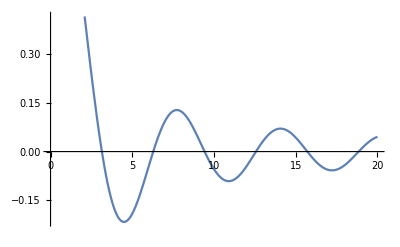

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496}

```mathematica
ClearAll["Global`*"];
n = 0;  
Plot[SphericalBesselJ[n,x],{x,0,20}]
x = {3,6,9,12,15,19};
besselzeros = roots /.FindRoot[SphericalBesselJ[n,roots],{roots,x}]
```

```mathematica
(* Alternative way of finding the bessel roots*)
(*Clear[besselzeros];
nRoots=5;
nBessel=3;
statenumber = 0;
SphBesselRoot[l_,k_]:=N[BesselJZero[l+1/2,k]];
n = Table[SphBesselRoot[l,i],{l,0,nBessel},{i,1,nRoots}];
besselzeros = n[[1]]*)
```

## Part II. Solving the god damn problem

Now that we have the roots, we can apply the same method as in Chapter 9 Problem 1.

```mathematica
h = 6.62607004 * 10^-34; (* Plankton's Constant *)
mo = 9.10938 * 10^-31; (* Effective mass of an electron *)
ℏ = h/(2*π);
nano = 1*10^-9;
e = 1.60217 * 10^-19;
r = 3*nano; (* Radius of sphere *)
NumberOfEnergies = 5;

En = N[ℏ^2/(2*mo)*((besselzeros/r)^2 )]; (* Energy values in Joules*)
EnEv = En/e; (* Energy values in electron volts *)

For[i=1,i<=NumberOfEnergies,i++,Print[i," lowest Energy Level is : \n\t",EnEv[[i]], " eV \t ", En[[i]], "J"]]
```

1 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

2 lowest Energy Level is : 
	0.167125 eV 	 2.67763×10^-20J

3 lowest Energy Level is : 
	0.376032 eV 	 6.02467×10^-20J

4 lowest Energy Level is : 
	0.668501 eV 	 1.07105×10^-19J

5 lowest Energy Level is : 
	1.04453 eV 	 1.67352×10^-19J

# Faster way:

Instead of finding the roots of the Bessel functions, we can actually see that for BesselJo, the zeros are nπ...thus our formula can change and we can create a function to find the energy at ANY state (ground, first excited, second excited, etc...).

```mathematica
Clear[n];
n = 1; (* ground state *)
```

```mathematica
EnJ[n_] = N[ℏ^2/(2*mo)*(((n*π)/r)^2 )](* energy in joules *)
Enev[n_] =  N[ℏ^2/(2*mo*e)*(((n*π)/r)^2 )] (* energy in electron volts *)
```

6.69408×10^-21

0.0417813

The above is a demonstration that the formula works, this matches our ground state, so let’s write our for loop again.

```mathematica
Clear[n];
For[n = 1, n ≤ NumberOfEnergies,n++, Print[n," lowest Energy Level is : \n\t",Enev[n], " eV \t ", EnJ[n], "J"]]
```

1 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

2 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

3 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

4 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

5 lowest Energy Level is : 
	0.0417813 eV 	 6.69408×10^-21J

## Same answers as above, except this is only one line of code (after writing constants).